```mathematica
(*Protocols*)
Ωp[t_]:= Ω0*Exp[- (t-tf/2-t0)^2/σ^2]
Ωs[t_]:= Ω0*Exp[- (t-tf/2+t0)^2/σ^2]
ΩpTR[t_,a_]:= Ω0*Exp[-(f[t, a]-tforiginal/2-tforiginal/10)^2/(tforiginal/6)^2]*( a -(a-1)*Cos[2*Pi*a*t/tforiginal])
ΩsTR[t_,a_]:= Ω0*Exp[-(f[t, a]-tforiginal/2+tforiginal/10)^2/(tforiginal/6)^2]*( a -(a-1)*Cos[2*Pi*a*t/tforiginal])
dΩp[t_]:=D[Ωp[b],b]/.b-> t
dΩs[t_]:=D[Ωs[b],b]/.b-> t
Ωa[t_]:=2*(dΩp[t]*Ωs[t]-Ωp[t]*dΩs[t])/(Ωp[t]^2 + Ωs[t]^2)
tforiginal = 10
f[t_, a_]:= a*t - (tforiginal/(2*Pi*a))*(a-1)*Sin[2*Pi*a*t/tforiginal]
df[t_,a_]:= a -(a-1)*Cos[2*Pi*a*t/tforiginal]
(*Parameters*)
ℏ = 1
Δ = 0
ti = 0
Ω0 = 2*Pi*3 (*MHz*)
tf = 0.1 (*μs*)
t0 = tf/10 (*μs*)
σ = tf/6 (*μs*)
a = tforiginal/tf
θ[Ωp_,Ωs_]:= ArcTan[Ωp/Ωs]
(*Eigenstates and Hamiltonian*)
v[θ_] := {Cos[θ],0,- Sin[θ]}
vCD[Ωp_,Ωs_,Ωa_]:= {-Ωs/(√(Abs[Ωa]^2+Abs[Ωp]^2+Abs[Ωs]^2)),-(ⅈ Ωa)/(√(Abs[Ωa]^2+Abs[Ωp]^2+Abs[Ωs]^2)),Ωp/(√(Abs[Ωa]^2+Abs[Ωp]^2+Abs[Ωs]^2))}
H[Ωp_,Ωs_,Δ_] := (ℏ/2)*{{0,Ωp,0},{Ωp,2*Δ,Ωs},{0,Ωs,0}}
(*Solutions Schrödinger's equation*)
Sol = NDSolve[{ⅈ*ℏ*c1'[t] ==(ℏ/2)*Ωp[t]*c2[t],ⅈ*ℏ*c2'[t] ==(ℏ/2)*Ωp[t]*c1[t]+(ℏ/2)*Ωs[t]*c3[t],ⅈ*ℏ*c3'[t] ==+(ℏ/2)*Ωs[t]*c2[t],c1[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti]^2 ],c2[ti]==0,c3[ti]==-Ωp[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti]^2 ] },{c1,c2,c3},{t,ti,tf}]
SolCD = NDSolve[{ⅈ*ℏ*c1CD'[t] ==(ℏ/2)*Ωp[t]*c2CD[t]+ⅈ*(ℏ/2)*Ωa[t]*c3CD[t],ⅈ*ℏ*c2CD'[t] ==(ℏ/2)*Ωp[t]*c1CD[t]+(ℏ/2)*Ωs[t]*c3CD[t],ⅈ*ℏ*c3CD'[t] ==-ⅈ*(ℏ/2)*Ωa[t]*c1CD[t]+(ℏ/2)*Ωs[t]*c2CD[t],c1CD[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti]^2 ],c2CD[ti]==0,c3CD[ti]==-Ωp[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti]^2 ] },{c1CD,c2CD,c3CD},{t,ti,tf}]
SolTR= NDSolve[{ⅈ*ℏ*c1TR'[t] ==(ℏ/2)*ΩpTR[t,a]*c2TR[t],ⅈ*ℏ*c2TR'[t] ==(ℏ/2)*ΩpTR[t,a]*c1TR[t]+(ℏ/2)*ΩsTR[t,a]*c3TR[t],ⅈ*ℏ*c3TR'[t] ==(ℏ/2)*ΩsTR[t,a]*c2TR[t],c1TR[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti]^2 ],c2TR[ti]==0,c3TR[ti]==-Ωp[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti]^2 ] },{c1TR,c2TR,c3TR},{t,ti,tf}]
(*Minimal fidelity?*)
(*Work quantum quench?*)
(*Mean energy? Zero*)
(*Fidelity with protocol time*)
```

10

1

0

0

6 π

0.1

0.01

0.0166667

100.

{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}}

{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}}

{{c1TR→InterpolatingFunction[…],c2TR→InterpolatingFunction[…],c3TR→InterpolatingFunction[…]}}

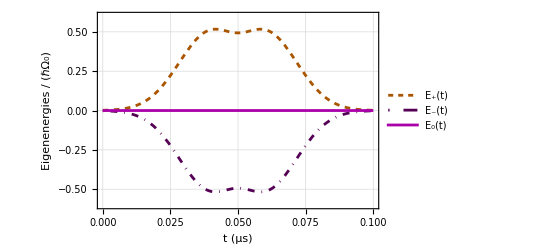

```mathematica
(*Autovalores*)
Show[Plot[0.5*Sqrt[Ωp[t]^2 + Ωs[t]^2]/Ω0, {t,ti,tf},PlotRange->{-0.6,0.6},PlotTheme-> "Detailed",PlotStyle-> {Darker[Orange], Dashing[0.01]},FrameLabel ->{"t (μs)", "Eigenenergies / (ℏΩ_0)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_+(t)",10]},LegendLayout->"Row"],{Right,0.94}]],Plot[-0.5*Sqrt[Ωp[t]^2 + Ωs[t]^2]/Ω0, {t,ti,tf},PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> {Darker[Purple], DotDashed},FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_-(t)",10]},LegendLayout->"Row"],{Right,0.86}]], Plot[0/Ω0,{t,ti,tf}, PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> Darker[Magenta],FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_0(t)",10]},LegendLayout->"Row"],{Right,0.78}]]]
```

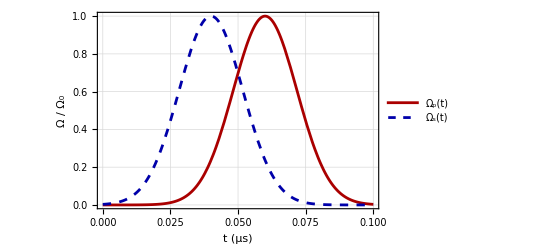

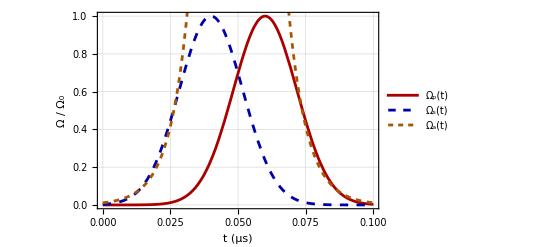

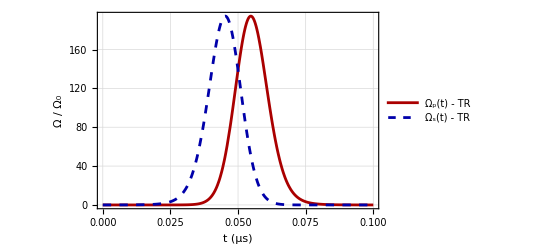

```mathematica
(*Reference protocols*)
Show[Plot[Ωp[t]/Ω0,{t,0,tf},PlotTheme-> "Detailed",PlotStyle-> Darker[Red],FrameLabel ->{"t (μs)", "Ω / Ω_0"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Right,0.94}]],Plot[Ωs[t]/Ω0,{t,0,tf},PlotTheme-> "Detailed",PlotStyle-> {Darker[Blue], Dashing[0.015]},FrameLabel ->{"t (μs)", "Ω / Ω_0"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Right,0.86}]]]
(*CD protocol*)
Show[Plot[Ωp[t]/Ω0,{t,0,tf},PlotTheme-> "Detailed",PlotStyle-> Darker[Red],FrameLabel ->{"t (μs)", "Ω / Ω_0"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Right,0.94}]],Plot[Ωs[t]/Ω0,{t,0,tf},PlotTheme-> "Detailed",PlotStyle-> {Darker[Blue], Dashing[0.015]},FrameLabel ->{"t (μs)", "Ω / Ω_0"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Right,0.86}]],Plot[Ωa[t]/Ω0,{t,0,tf},PlotTheme-> "Detailed",PlotStyle-> {Darker[Orange],Dashing[0.01]},FrameLabel ->{"t (μs)", "Ω / Ω_0"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_a(t)",10]},LegendLayout->"Row"],{Right,0.78}]]]
(*Time-rescaled protocols*)
Show[Plot[ΩpTR[t,a]/Ω0,{t,0,tf},PlotTheme-> "Detailed",PlotStyle-> Darker[Red],FrameLabel ->{"t (μs)", "Ω / Ω_0"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - TR",10]},LegendLayout->"Row"],{Right,0.94}]],Plot[ΩsTR[t,a]/Ω0,{t,0,tf},PlotTheme-> "Detailed",PlotStyle-> {Darker[Blue], Dashing[0.015]},FrameLabel ->{"t (μs)", "Ω / Ω_0"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t) - TR",10]},LegendLayout->"Row"],{Right,0.86}]]]
```

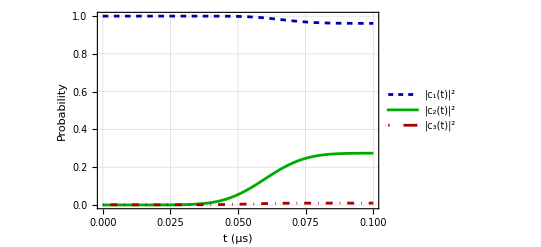

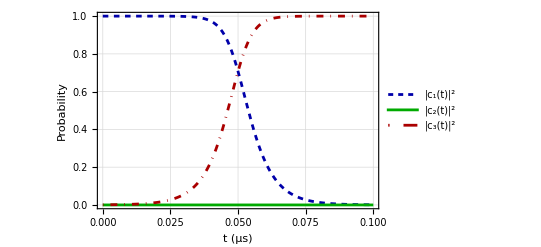

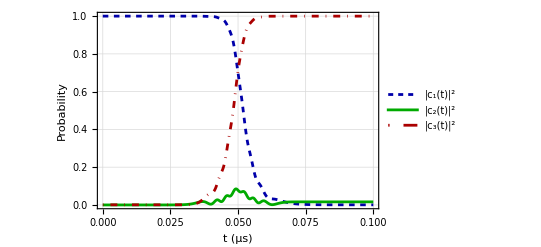

```mathematica
ψ[t_]:= {{Evaluate[c1[t]/.Part[Flatten[Sol],1]]},{Evaluate[c2[t]/.Part[Flatten[Sol],2]]},{Evaluate[c3[t]/.Part[Flatten[Sol],3]]}}
ψCD[t_]:= {Evaluate[c1CD[t]/.Part[Flatten[SolCD],1]],Evaluate[c2CD[t]/.Part[Flatten[SolCD],2]],Evaluate[c3CD[t]/.Part[Flatten[SolCD],3]]}
ψTR[t_]:= {Evaluate[c1TR[t]/.Part[Flatten[SolTR],1]],Evaluate[c2TR[t]/.Part[Flatten[SolTR],2]],Evaluate[c3TR[t]/.Part[Flatten[SolTR],3]]}
ρ[t_]:= ψ[t].ConjugateTranspose[ψ[t]]
(*Evolution of the probabilities during the protocol*)
(*Probabiliies with reference protocols*)
Show[Plot[Abs[Evaluate[c1[t]/.Part[Flatten[Sol],1]]], {t,ti,tf},PlotRange->{0,1},PlotStyle->{Darker[Blue],Dashing[0.01]},PlotTheme-> "Detailed",FrameLabel ->{"t (μs)", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t)|^2",10]},LegendLayout->"Row"],{Right,0.32}]],
Plot[Abs[Evaluate[c2[t]/.Part[Flatten[Sol],2]]], {t,ti,tf},PlotTheme-> "Detailed",PlotStyle->{Darker[Green]},FrameLabel ->{"t", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t)|^2",10]},LegendLayout->"Row"],{Right,0.24}]],
Plot[Abs[Evaluate[c3[t]/.Part[Flatten[Sol],3]]], {t,ti,tf},PlotTheme-> "Detailed",PlotStyle->{Darker[Red], DotDashed},FrameLabel ->{"t", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t)|^2",10]},LegendLayout->"Row"],{Right,0.16}]]]
(*Probabilities in CD driving*)
Show[Plot[Abs[Evaluate[c1CD[t]/.Part[Flatten[SolCD],1]]], {t,ti,tf},PlotStyle->{Darker[Blue],Dashing[0.01]},PlotTheme-> "Detailed",FrameLabel ->{"t (μs)", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t)|^2",10]},LegendLayout->"Row"],{Right,0.32}]],
Plot[Abs[Evaluate[c2CD[t]/.Part[Flatten[SolCD],2]]], {t,ti,tf},PlotTheme-> "Detailed",PlotStyle->{Darker[Green]},FrameLabel ->{"t", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t)|^2",10]},LegendLayout->"Row"],{Right,0.24}]],
Plot[Abs[Evaluate[c3CD[t]/.Part[Flatten[SolCD],3]]], {t,ti,tf},PlotTheme-> "Detailed",PlotStyle->{Darker[Red], DotDashed},FrameLabel ->{"t", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t)|^2",10]},LegendLayout->"Row"],{Right,0.16}]]]
(*Probabilities in TR*)
Show[Plot[Abs[Evaluate[c1TR[t]/.Part[Flatten[SolTR],1]]], {t,ti,tf},PlotStyle->{Darker[Blue],Dashing[0.01]}, PlotRange->All,PlotTheme-> "Detailed",PlotStyle->Darker[Green],FrameLabel ->{"t (μs)", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t)|^2",10]},LegendLayout->"Row"],{Right,0.32}]],
Plot[Abs[Evaluate[c2TR[t]/.Part[Flatten[SolTR],2]]], {t,ti,tf}, PlotRange->All,PlotTheme-> "Detailed",PlotStyle->Darker[Green],FrameLabel ->{"t", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t)|^2",10]},LegendLayout->"Row"],{Right,0.24}]],
Plot[Abs[Evaluate[c3TR[t]/.Part[Flatten[SolTR],3]]], {t,ti,tf}, PlotRange->All,PlotTheme-> "Detailed",PlotStyle->{Darker[Red], DotDashed},FrameLabel ->{"t", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t)|^2",10]},LegendLayout->"Row"],{Right,0.16}]]]
```

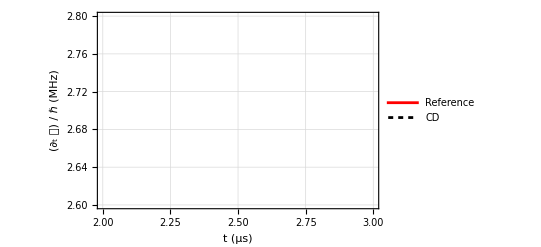

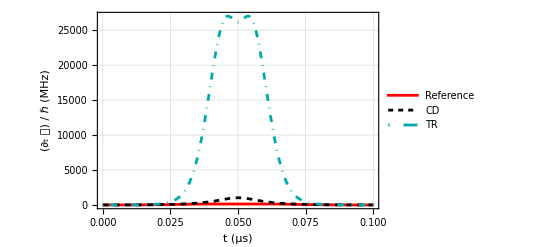

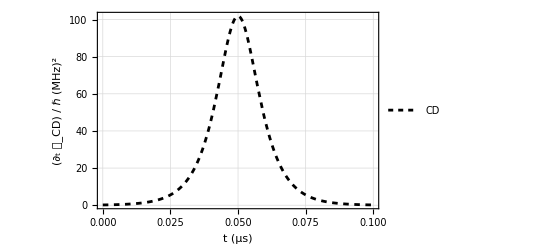

```mathematica
(*Cost*)
(*Inset*)
fig = Show[Plot[Sqrt[Ωp[t]^2+ Ωs[t]^2]/(Sqrt[2]*tf), {t,ti,tf}, PlotRange->{{2,3},{2.6,2.8}},PlotTheme-> "Detailed",PlotStyle-> Red,FrameLabel ->{"t (μs)", "(∂_t 𝒞) / ℏ (MHz)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Reference",10]},LegendLayout->"Row"],{Right,0.20}]],Plot[Sqrt[Ωp[t]^2+ Ωs[t]^2 + Ωa[t]^2]/(Sqrt[2]*tf), {t,ti,tf}, PlotStyle->{Black, Dashing[0.01]}, PlotRange->All,PlotTheme-> "Detailed",PlotStyle->Darker[Green],FrameLabel ->{"t (μs)", "dt(sqrt2C/ℏ)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["CD",10]},LegendLayout->"Row"],{Right,0.12}]]
]
(*Cost Santos & Sarandy*)
Show[Plot[Sqrt[Ωp[t]^2+ Ωs[t]^2]/(Sqrt[2]*tf), {t,ti,tf}, PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> Red,FrameLabel ->{"t (μs)", "(∂_t 𝒞) / ℏ (MHz)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Reference",10]},LegendLayout->"Row"],{Right,0.94}]],Plot[Sqrt[Ωp[t]^2+ Ωs[t]^2 + Ωa[t]^2]/(Sqrt[2]*tf), {t,ti,tf}, PlotStyle->{Black, Dashing[0.01]}, PlotRange->All,PlotTheme-> "Detailed",PlotStyle->Darker[Green],FrameLabel ->{"t (μs)", "dt(sqrt2C/ℏ)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["CD",10]},LegendLayout->"Row"],{Right,0.86}]],Plot[Sqrt[ΩpTR[t,a]^2+ ΩsTR[t,a]^2]/(Sqrt[2]*tf), {t,ti,tf}, PlotRange->All,PlotTheme-> "Detailed",PlotStyle->{Darker[Cyan], DotDashed},FrameLabel ->{"t (μs)", "∂𝒞/∂t"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["TR",10]},LegendLayout->"Row"],{Right,0.78}]]]
(*Cost Zheng & Funo*)
Plot[Sqrt[Ωa[t]^2]/Sqrt[2], {t,ti,tf}, PlotRange->All,PlotTheme-> "Detailed",PlotStyle->{Black, Dashing[0.01]},FrameLabel ->{"t (μs)", "(∂_t 𝒞_CD) / ℏ (MHz)^2"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["CD",10]},LegendLayout->"Row"],{Right,0.94}]]
```

```mathematica
Sqrt[Ωp[tf/2]^2+ Ωs[tf/2]^2 + Ωa[tf/2]^2]
Sqrt[Ωa[tf/2]^2]
Sqrt[Ωp[tf/2]^2+ Ωs[tf/2]^2 ]
```

145.196

144.

18.5982

```mathematica
F[t_]:= Abs[v[θ[Ωp[t],Ωs[t]]].ψ[t]]
ℰ[t_]:= ℏ*(Ωp[t]*Re[Part[ψ[t],1]*Conjugate[Part[ψ[t],2]]]+ Ωs[t]*Re[Part[ψ[t],3]*Conjugate[Part[ψ[t],2]]])
FCD[t_]:= Abs[v[θ[Ωp[t],Ωs[t]]].ψCD[t]]
FTR[t_]:= Abs[v[θ[ΩpTR[t,a],ΩsTR[t,a]]].ψTR[t]]
```

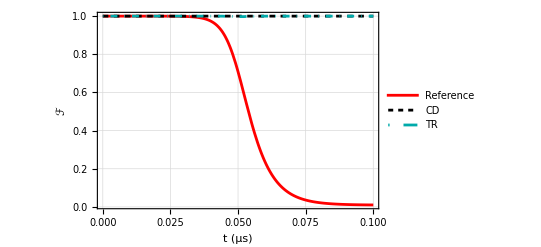

{0.0103162}

```mathematica
(*Fidelity during the protocol*)
Show[Plot[F[t],{t,ti,tf}, PlotRange->All,PlotStyle->Red,PlotTheme-> "Detailed",FrameLabel ->{"t (μs)", "ℱ"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Reference",10]},LegendLayout->"Row"],{Right,0.22}]], Plot[FCD[t],{t,ti,tf}, PlotRange->All,PlotTheme-> "Detailed",PlotStyle->{Black, Dashing[0.01]},FrameLabel ->{"t", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["CD",10]},LegendLayout->"Row"],{Right,0.14}]],Plot[FTR[t],{t,ti,tf}, PlotRange->All,PlotStyle->{Darker[Cyan], DotDashed},PlotTheme-> "Detailed",FrameLabel ->{"t (μs)", "ℱ"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["TR",10]},LegendLayout->"Row"],{Right,0.06}]]]
(*Fidelity at the end of the process for the reference protocol*)
F[tf]
```

```mathematica
(*Cost with protocol time*)
Tmin = 0.1
Tmax = 10.0
Ωp2[t_,tf_]:= Ω0*Exp[- (t-tf/2-tf/10 )^2/( tf/6 )^2]
Ωs2[t_,tf_]:= Ω0*Exp[- (t-tf/2+tf/10 )^2/( tf/6 )^2]
dΩp2[t_,tf_]:=D[Ωp2[b,tf],b]/.b-> t
dΩs2[t_,tf_]:=D[Ωs2[b,tf],b]/.b-> t
Ωa2[t_,tf_]:=2*(dΩp2[t,tf]*Ωs2[t,tf]-Ωp2[t,tf]*dΩs2[t,tf])/(Ωp2[t,tf]^2 + Ωs2[t,tf]^2)
Cost [tf_] := 1/(tf)*NIntegrate[Sqrt[Ωp2[t,tf]^2+Ωs2[t,tf]^2],{t,ti,tf}]
CostCD[tf_] := 1/(tf)*NIntegrate[Sqrt[Ωp2[t,tf]^2+Ωs2[t,tf]^2 + Ωa2[t,tf]^2],{t,ti,tf}]
CostTR [tf_] := 1/(tf)*NIntegrate[Sqrt[ΩpTR[t,tforiginal/tf]^2+ΩsTR[t,tforiginal/tf]^2],{t,ti,tf}]
```

0.1

10.

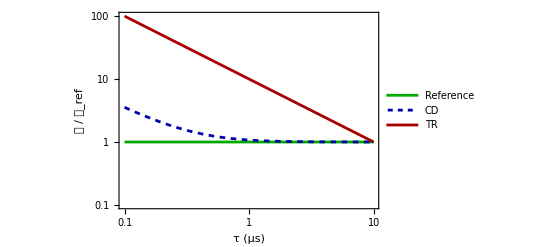

```mathematica
Show[LogLogPlot[Cost[tf]/9.418871042823335,{tf,Tmin,Tmax},GridLines-> Automatic, Frame-> True,PlotRange->{{Tmin-0.001,Tmax},{0.1,100}}, PlotStyle->Darker[Green],FrameLabel ->{"τ (μs)", "𝒞 / 𝒞_ref"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Reference",10]},LegendLayout->"Row"],{Right,0.94}],Ticks->{Table[{10^i,Superscript[10,i]},{i,-1,5}],Table[{10^i,Superscript[10,i]},{i,-2,6}]}],LogLogPlot[CostCD[tf]/9.418871042823335,{tf,Tmin,Tmax},PlotRange-> All,PlotTheme-> "Detailed",PlotStyle->{Darker[Blue], Dashing[0.01]},FrameLabel ->{"τ (μs)", "𝒞"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["CD",10]},LegendLayout->"Row"],{Right,0.86}]],LogLogPlot[CostTR[tf]/9.418871042823335,{tf,Tmin,Tmax}, PlotRange-> All,PlotTheme-> "Detailed",PlotStyle->Darker[Red],FrameLabel ->{"τ (μs)", "𝒞"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["TR",10]},LegendLayout->"Row"],{Right,0.78}]]]
```

```mathematica
Subscript[𝒞,ref]
```

𝒞_ref

```mathematica
Cost[tf]
```

9.41887

0

10

1

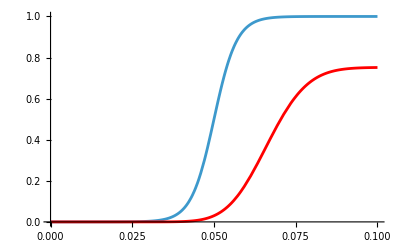

```mathematica
(*Atom Hamiltonian*)
En1 = 0
En2 = 10
En3 = 1
Show[Plot[Part[v[θ[Ωp[t],Ωs[t]]],1]*Conjugate[Part[v[θ[Ωp[t],Ωs[t]]],1]]*En1 + Part[v[θ[Ωp[t],Ωs[t]]],2]*Conjugate[Part[v[θ[Ωp[t],Ωs[t]]],2]]*En2+Part[v[θ[Ωp[t],Ωs[t]]],3]*Conjugate[Part[v[θ[Ωp[t],Ωs[t]]],3]]*En3,{t,ti,tf}],
Plot[Part[ψ[t],1]*Conjugate[Part[ψ[t],1]]*En1 + Part[ψ[t],2]*Conjugate[Part[ψ[t],2]]*En2+Part[ψ[t],3]*Conjugate[Part[ψ[t],3]]*En3,{t,ti,tf}, PlotStyle->Red],Plot[Part[vCD[Ωp[t],Ωs[t],Ωa[t]],1]*Conjugate[Part[vCD[Ωp[t],Ωs[t],Ωa[t]],1]]*En1 + Part[vCD[Ωp[t],Ωs[t],Ωa[t]],2]*Conjugate[Part[vCD[Ωp[t],Ωs[t],Ωa[t]],2]]*En2+Part[vCD[Ωp[t],Ωs[t],Ωa[t]],3]*Conjugate[Part[vCD[Ωp[t],Ωs[t],Ωa[t]],3]]*En3,{t,ti,tf}, PlotStyle->Darker[Green]]]
```

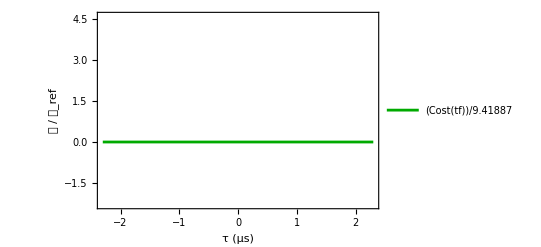

```mathematica
LogLogPlot[Cost[tf]/9.418871042823335,{tf,Tmin,Tmax},PlotRange-> {{Tmin,Tmax},{0.1,100}},PlotTheme->"Detailed",PlotStyle->Darker[Green],FrameLabel ->{"τ (μs)", "𝒞 / 𝒞_ref"},FrameTicks->None,Ticks->{Table[{10^i,Superscript[10,i]},{i,0,5}],Table[{10^i,Superscript[10,i]},{i,-1,6}]}]
```

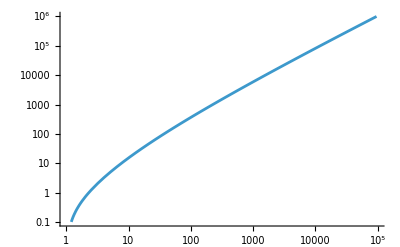

```mathematica
LogLogPlot[Log[x!],{x,1,10^5},PlotRange->{{0,10^5},{10^-1,10^6}},Ticks->{Table[{10^i,Superscript[10,i]},{i,0,5}],Table[{10^i,Superscript[10,i]},{i,-1,6}]}]
```

```mathematica
m = 50
ΔT = (Tmax-Tmin)/m
Sol2 = Table[NDSolve[{ⅈ*ℏ*c1'[t] ==(ℏ/2)*Ωp2[t,tf]*c2[t],ⅈ*ℏ*c2'[t] ==(ℏ/2)*Ωp2[t,tf]*c1[t]+(ℏ/2)*Ωs2[t,tf]*c3[t],ⅈ*ℏ*c3'[t] ==+(ℏ/2)*Ωs2[t,tf]*c2[t],c1[ti]==Ωs2[ti,tf]/Sqrt[Ωs2[ti,tf]^2 + Ωp2[ti,tf]^2 ],c2[ti]==0,c3[ti]==-Ωp2[ti,tf]/Sqrt[Ωs2[ti,tf]^2 + Ωp2[ti,tf]^2 ] },{c1,c2,c3},{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

50

0.198

{{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}}}

```mathematica
Fid = Table[Abs[v[θ[Ωp2[t,(Tmin + (n-1)*ΔT)],Ωs2[t,(Tmin + (n-1)*ΔT)]]]. {Evaluate[c1[t]/.Part[Flatten[Part[Sol2,n]],1]],Evaluate[c2[t]/.Part[Flatten[Part[Sol2,n]],2]],Evaluate[c3[t]/.Part[Flatten[Part[Sol2,n]],3]]}]/.t-> (Tmin + (n-1)*ΔT),{n, 1, Length[Sol2],1}]
time = Table[ (Tmin + (n-1)*ΔT),{n, 1, Length[Sol2],1}]
```

{0.0103162,0.0771929,0.197476,0.349031,0.507148,0.650923,0.7674,0.852471,0.90898,0.943436,0.962936,0.973295,0.978528,0.981207,0.982992,0.984937,0.987535,0.990711,0.993971,0.99672,0.998583,0.999554,0.99991,0.999987,0.999989,0.999948,0.999816,0.999592,0.999369,0.999277,0.99938,0.999621,0.999865,0.999991,0.999976,0.999891,0.999837,0.999866,0.999945,0.999998,0.999974,0.999887,0.999806,0.999794,0.999858,0.999949,0.999999,0.999978,0.999912,0.999861,0.999867}

{0.1,0.298,0.496,0.694,0.892,1.09,1.288,1.486,1.684,1.882,2.08,2.278,2.476,2.674,2.872,3.07,3.268,3.466,3.664,3.862,4.06,4.258,4.456,4.654,4.852,5.05,5.248,5.446,5.644,5.842,6.04,6.238,6.436,6.634,6.832,7.03,7.228,7.426,7.624,7.822,8.02,8.218,8.416,8.614,8.812,9.01,9.208,9.406,9.604,9.802,10.}

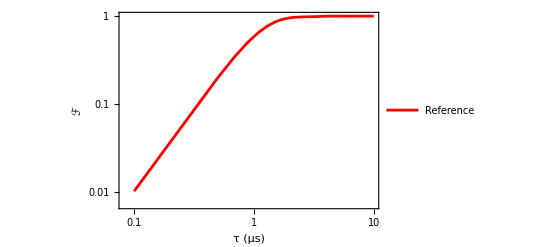

```mathematica
ListLogLogPlot[Transpose[{time, Flatten[Fid]}], Joined-> True, PlotRange->All,PlotStyle->Red,PlotTheme-> "Detailed",FrameLabel ->{"τ (μs)", "ℱ"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Reference",10]},LegendLayout->"Row"],{Right,0.10}]]
```

```mathematica
Simplify[Abs[v[θ[Ωp[tf],Ωs[tf]]].v[θ[Ωp[ti],Ωs[ti]]]]]
```

0.00149317

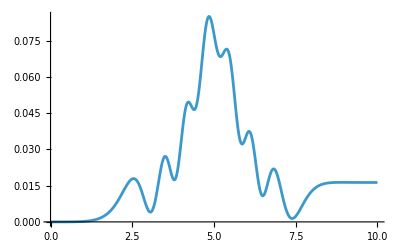

```mathematica
Plot[Abs[Evaluate[c2[t]/.Part[Flatten[Part[Sol2,Length[Sol2]]],2]]], {t,ti,Tmax}]
```

```mathematica
n = Length[Sol2]
Abs[v[θ[Ωp2[t,(Tmin + (n-1)*ΔT)],Ωs2[t,(Tmin + (n-1)*ΔT)]]]. {Evaluate[c1[t]/.Part[Flatten[Part[Sol2,n]],1]],Evaluate[c2[t]/.Part[Flatten[Part[Sol2,n]],2]],Evaluate[c3[t]/.Part[Flatten[Part[Sol2,n]],3]]}]/.t-> (Tmin + (n-1)*ΔT)
```

51

0.999867

```mathematica
v[θ[Ωp[t],Ωs[t]]]
(Tmin + (n-1)*ΔT)
```

{1/(√(1+ⅇ^(-7200. (-0.06+t)^2+7200. (-0.04+t)^2))),0,-(ⅇ^(-3600. (-0.06+t)^2+3600. (-0.04+t)^2))/(√(1+ⅇ^(-7200. (-0.06+t)^2+7200. (-0.04+t)^2)))}

10.